```mathematica
Module[{directory=SystemDialogInput["Directory"]},If[directory=!=$Canceled,SetDirectory[directory]]]
```

/Users/mepistol/People/Mats-Erik/IsospectralGraphs/Mathematica programs/Graphs

```mathematica
ReadMatrix8[n_]:=Do[ReadLine["8graphs"];
m8[j]={IntegerDigits[#,10,8]&@Read["8graphs",Number],
IntegerDigits[#,10,8]&@Read["8graphs",Number],IntegerDigits[#,10,8]&@Read["8graphs",Number],IntegerDigits[#,10,8]&@Read["8graphs",Number],IntegerDigits[#,10,8]&@Read["8graphs",Number],
IntegerDigits[#,10,8]&@Read["8graphs",Number],IntegerDigits[#,10,8]&@Read["8graphs",Number],IntegerDigits[#,10,8]&@Read["8graphs",Number]},{j,1,n}];

ReadMatrix9[n_]:=Do[ReadLine["9graphs"];
m9[j]={IntegerDigits[#,10,9]&@Read["9graphs",Number],
IntegerDigits[#,10,9]&@Read["9graphs",Number],
IntegerDigits[#,10,9]&@Read["9graphs",Number],IntegerDigits[#,10,9]&@Read["9graphs",Number],IntegerDigits[#,10,9]&@Read["9graphs",Number],
IntegerDigits[#,10,9]&@Read["9graphs",Number],IntegerDigits[#,10,9]&@Read["9graphs",Number],IntegerDigits[#,10,9]&@Read["9graphs",Number],IntegerDigits[#,10,9]&@Read["9graphs",Number]},{j,1,n}];
```

```mathematica
Close["8graphs"];
Close["9graphs"];
ReadMatrix8[11117] (* There are 11117 graphs with eight vertices and 261080 graphs with nine vertices *)
ReadMatrix9[261080]
```

```mathematica
MatrixForm@m9[2] (* Test *)
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0)

```mathematica
graph8table=Table[AdjacencyGraph@m8[i],{i,1,11117}]; (* This takes a minute or so. *)
graph9table=Table[AdjacencyGraph@m9[i],{i,1,261080}];
```

```mathematica
graph9table[[11000]] (* Test *)
```

```mathematica
isop8=IsoCharacteristicPolynomialPairs[graph8table]; (* This takes hours. *)
isop9=IsoCharacteristicPolynomialPairs[graph9table];
```

```mathematica
tentative8pairs=Table[IsospectralPairs[isop8[[i]]],{i,1,Length@isop8}]; (* This takes maybe ten minutes. *)
tentative9pairs=Table[IsospectralPairs[isop9[[i]]],{i,1,Length@isop9}];
```

tentative8pairs, 91 of them

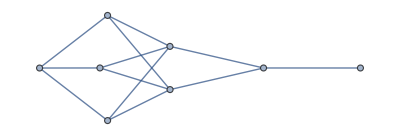
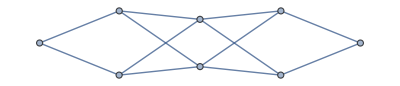
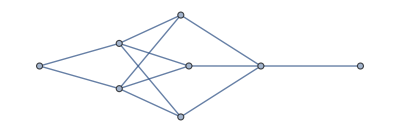
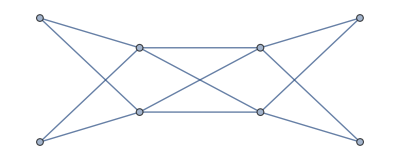
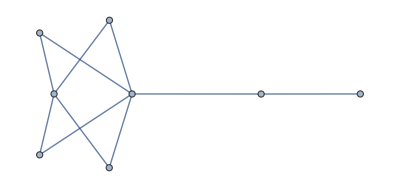
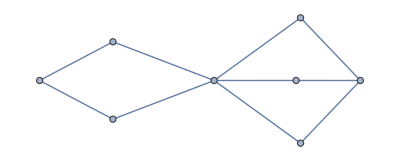
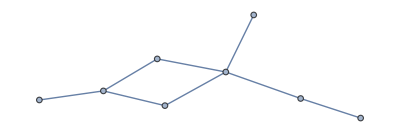
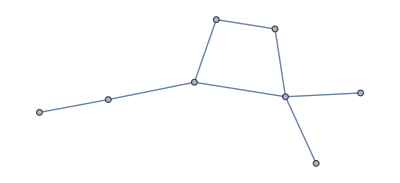

{{},{},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{},{},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{},{},{{-Graphics-,-Graphics-}},{},{},{},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{},{},{},{},{},{},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{},{},{},{},{},{},{},{},{},{},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{},{{-Graphics-,-Graphics-,-Graphics-}}}

tentative9pairs, 316 of them

```mathematica
{{},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{},{},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{},{},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{},{},{},{},{},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{},{},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{},{{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-}}}
```

Checked pairs with eight vertices below, beautified.

```mathematica
cp={{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

Figures of triplets for the paper.

```mathematica
GraphPlot[#,GraphLayout->"SpringElectricalEmbedding",PlotStyle->Thickness[0.01]]&/@{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
GraphPlot[#,GraphLayout->"SpringElectricalEmbedding",PlotStyle->Thickness[0.01]]&/@{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
GraphPlot[#,GraphLayout->"SpringElectricalEmbedding",PlotStyle->Thickness[0.01]]&/@{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

Checked isospectral sets with nine vertices

```mathematica
ninevertices={{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}};
```

Checking the isospectral sets with nine vertices by computer.

```mathematica
Length@ninevertices
```

316

```mathematica
SDeterminantD[x_]:=((DeterminantD[x]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1})  (* This needs a small check and rewrite of the rule. *)
```

Do[If[SDeterminantD@ninevertices[[i,1]]==SDeterminantD@ninevertices[[i,2]],Print[1],Print[0]],i,1,316]
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1

Plotting the isospectral sets with nine vertices.

```mathematica
fig=Small@ninevertices
```

```mathematica
fig2=Map@(GraphPlot[#,GraphLayout->"SpringEmbedding"]&)/@fig; (* Different GraphLayout to avoid overlapping edges. *)
```

```mathematica
Partition[fig2,UpTo[80]]
```

{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
triplets=Select[ninevertices,Length@#==3&];
(* Map@(GraphPlot[#,GraphLayout->"SpringElectricalEmbedding"]&)/@triplets *)
```

```mathematica
triplets
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

Below are the triplets with nine vertices where possible overlapping edges have been checked. There shouldn’t be any more.

```mathematica
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}
```